Sandia QSCOUT Data Analysis Single State Prep Version

	First, run the library at the bottom. Then you can tweak the Main Cells. In all cases, we’re preparing states of the LMG model with V=Sqrt[3], W = Sqrt[2] and ν_a=ν_b=0. The data was run on a JAQAL simulator with some noise. Measurements were done in the clique format. Shot numbers were 2^8 but the data was saved in a “single-estimate” format. This is different than the IBM ones which had 2^13 each.
	
	Instructions: 
	1.) Run the Library cell.
	2.) Put in the correct filepaths for the 1-, 2- and 3-qubit single state preparation files. These are fp1, fp2 and fp3 in the Main Cell.
	3.) Run the main cell!

Single Point Preparation:
	This cell takes the files you feed it, analyzes them and outputs some data visualizations. The expectation values are -0.6158ϵ for 1 qubit, -1.6164ϵ for 2 qubits and -2.6286 for 3 qubits.

```mathematica
(* Main Cell *)
ClearAll[pldata,rerror]
pldata[explist_,spacing_]:=(step1=HistogramList[explist,spacing];
Transpose[{step1[[1,1;;Length[step1[[1]]]-1]],step1[[2]]/Total[step1[[2]]]}])
rerror[expected_,observed_]:=Abs[(observed-expected)/expected]; (* The relative error's absolute value. *)
fp1="/Users/krobbi02/Documents/QI_Research/SandiaFolder/NoisyJaqalData/point/1/single_point_eval.txt";
(* 2 QUBIT: Where to find the datafile you want to read. *)
fp2="/Users/krobbi02/Documents/QI_Research/SandiaFolder/NoisyJaqalData/point/2/single_point_eval.txt";
(* 3 QUBIT: Where to find the datafile you want to read. *)
fp3="/Users/krobbi02/Documents/QI_Research/SandiaFolder/NoisyJaqalData/point/3/single_point_eval.txt";
(* 1 QUBIT: Where to find the datafile you want to read. *)
th1=-0.6157688743457477; (* The theoretical expectation value for 1 qubit. *)
th2=-1.6164000911382201; (* The theoretical expectation value for 2 qubits. *)
th3=-2.6286138040619313; (* The theoretical expectation value for 3 qubits. *)
V=Sqrt[3.]; (* Sets the strength of the V interaction parameter. The interesting one! Don't change unless you change it in the code. *)
W=Sqrt[2.];(* Sets the strength of the W interaction parameter. Don't change unless you change it in the code. *)
νa=0;(* Sets the number of unpaired particles in the "a" mode to 0. Don't change unless you change it in the code. *)
νb=0;(* Sets the number of unpaired particles in the "b" mode to 0. Don't change unless you change it in the code. *)
(* Analyzing 1 Qubit Data *)
stringlist=ToExpression[StringReplace[ReadString[fp1],{"["->"{","]"->"}","'"->"\""}]];
listlist1=Table[Flatten@ToExpression@StringSplit[stringlist[[i,j]],""],{i,1,Length[stringlist]},{j,1,Length[stringlist[[1]]]}]; 
(* Prepping the string for digestion by outputeaters. *)
reslist1=Table[outputeater1[listlist1[[1,i]]]+outputeater2[listlist1[[2,i]]],{i,1,Length[listlist1[[1]]]}]; (* List of 1-qubit ⟨H⟩ estimates. *)
(* Analyzing 2 Qubit Data *)
stringlist=ToExpression[StringReplace[ReadString[fp2],{"["->"{","]"->"}","'"->"\""}]];(* Prepping the string for digestion by outputeaters. *)
listlist2=Table[Flatten@ToExpression@StringSplit[stringlist[[i,j]],""],{i,1,Length[stringlist]},{j,1,Length[stringlist[[1]]]}]; 
reslist2=Table[outputeater1[listlist2[[1,i]]]+outputeater2[listlist2[[2,i]]]+outputeater3[listlist2[[3,i]]],{i,1,Length[listlist2[[1]]]}];(* List of 2-qubit ⟨H⟩ estimates. *)
(* Analyzing 3 Qubit Data *)
stringlist=ToExpression[StringReplace[ReadString[fp3],{"["->"{","]"->"}","'"->"\""}]];(* Prepping the string for digestion by outputeaters. *)
listlist3=Table[Flatten@ToExpression@StringSplit[stringlist[[i,j]],""],{i,1,Length[stringlist]},{j,1,Length[stringlist[[1]]]}]; 
reslist3=Table[outputeater1[listlist3[[1,i]]]+outputeater2[listlist3[[2,i]]]+outputeater3[listlist3[[3,i]]]+outputeater4[listlist3[[4,i]]],{i,1,Length[listlist3[[1]]]}];(* List of 3-qubit ⟨H⟩ estimates. *)
```

The 1-Qubit data had an expectation value of -0.613802ϵ which has a relative error of -0.3%.

The 2-Qubit data had an expectation value of -1.48121ϵ which has a relative error of -8.4%.

The 3-Qubit data had an expectation value of -2.20041ϵ which has a relative error of -16.3%.

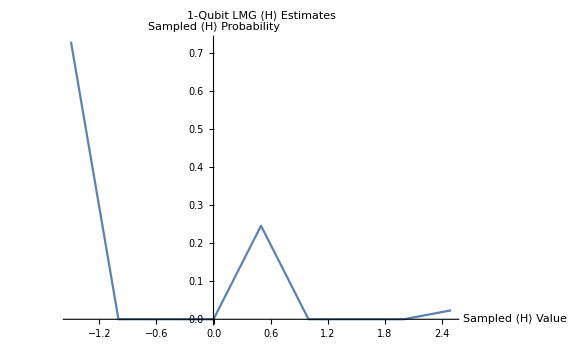

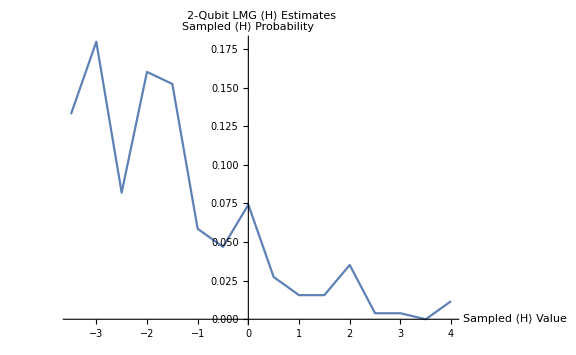

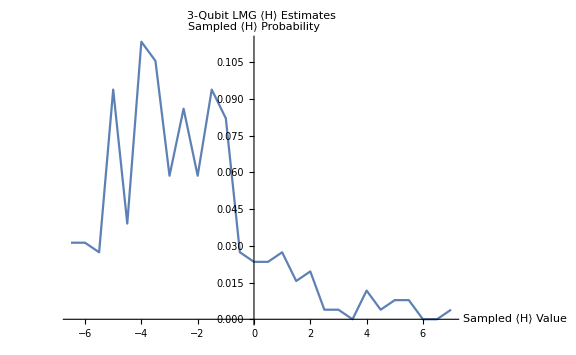

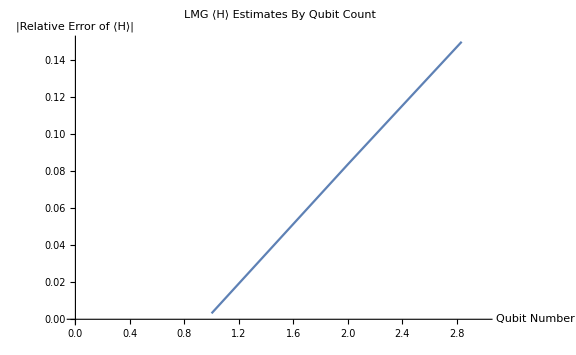

```mathematica
(* Visualizing Data *)
Print[Style["The 1-Qubit data had an expectation value of ",FontSize->25],Style[Mean[reslist1],FontSize->25],Style["ϵ which has a relative error of ",FontSize->25],Style[NumberForm[100*(Mean[reslist1]-th1)/th1,{5,1}],FontSize->25],Style["%.",FontSize->25]]
Print[Style["The 2-Qubit data had an expectation value of ",FontSize->25],Style[Mean[reslist2],FontSize->25],Style["ϵ which has a relative error of ",FontSize->25],Style[NumberForm[100*(Mean[reslist2]-th2)/th2,{5,1}],FontSize->25],Style["%.",FontSize->25]]
Print[Style["The 3-Qubit data had an expectation value of ",FontSize->25],Style[Mean[reslist3],FontSize->25],Style["ϵ which has a relative error of ",FontSize->25],Style[NumberForm[100*(Mean[reslist3]-th3)/th3,{5,1}],FontSize->25],Style["%.",FontSize->25]]
bw={.5}; (* Pick a bin width. *)
tf=25; (* Plot title (label) font size. *)
af=17;(* Axes label font size. *)
ListPlot[pldata[reslist1,bw],Joined->True,ImageSize->Large,AxesLabel->{Style["Sampled ⟨H⟩ Value",FontSize->af],Style["Sampled ⟨H⟩ Probability",FontSize->af]},PlotLabel->Style["1-Qubit LMG ⟨H⟩ Estimates",FontSize->tf]]
ListPlot[pldata[reslist2,bw],Joined->True,ImageSize->Large,AxesLabel->{Style["Sampled ⟨H⟩ Value",FontSize->af],Style["Sampled ⟨H⟩ Probability",FontSize->af]},PlotLabel->Style["2-Qubit LMG ⟨H⟩ Estimates",FontSize->tf]]
ListPlot[pldata[reslist3,bw],Joined->True,ImageSize->Large,AxesLabel->{Style["Sampled ⟨H⟩ Value",FontSize->af],Style["Sampled ⟨H⟩ Probability",FontSize->af]},PlotLabel->Style["3-Qubit LMG ⟨H⟩ Estimates",FontSize->tf]]
ListPlot[{{1,rerror[th1,Mean[reslist1]]},{2,rerror[th2,Mean[reslist2]]},{3,rerror[th3,Mean[reslist3]]}},Joined->True,ImageSize->Large,AxesLabel->{Style["Qubit Number",FontSize->af],Style["|Relative Error of ⟨H⟩|",FontSize->af]},PlotLabel->Style["LMG ⟨H⟩ Estimates By Qubit Count",FontSize->tf],PlotRange->{{0,3},{0,0.15}}]
```

```mathematica
(* Library *)

ClearAll[h,vec,M,νa,νb,V,W,id,x,y,z,sig,na,nb,nanb,vad,vbd,kp,ham,nterms,alth1,alth2,idenc,z1c,zMc,zjc,zijc,altn,xjc,yjc,yzjc,xzjc,exterms,hamterms,hmaker,hamterms2,hamtermsnoy,cl1maker,cl2maker,cl3maker,cl4maker,unit,diagmat,cl1diag,cl2diag,cl3diag,cl4diag,dict1,dict2,dict3,dict4]
ClearAll[efcl1,efcl2,efcl3,efcl4,efdic1,efdic2,efdic3,efdic4,outputeater1,outputeater2,outputeater3,outputeater4]
h[M_]:=If[M==1,{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},KroneckerProduct@@Array[HadamardMatrix[2]&,M]];
c2not={{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}};
{id,x,y,z}=Table[PauliMatrix[i],{i,0,3}];
vec[len_,entry_]:=ReplacePart[Array[0&,len],entry->1]
kp[ps__]:=(
If[Length[{ps}]==1,sig[[ps+1]],(
KroneckerProduct@@Table[sig[[{ps}[[i]]+1]],{i,1,Length[{ps}]}])]) (* Makes Kronecker Products easier.  Just input some numbers from 0 to 3 separated by commas! *)
sig={id,x,y,z};
na[M_]:=(νa/2(IdentityMatrix[2^M]+kp@@(3*vec[M,1]))+(νa+2M)/2(IdentityMatrix[2^M]-kp@@(3*vec[M,M]))+1/4*Sum[(νa+2k)((IdentityMatrix[2^M]-kp@@(3vec[M,k])).(IdentityMatrix[2^M]+kp@@(3vec[M,k+1]))),{k,1,M-1}]) (* The Subscript[n, a] operator. *)
nb[M_]:=((νb+2M)/2(IdentityMatrix[2^M]+kp@@(3*vec[M,1]))+νb/2(IdentityMatrix[2^M]-kp@@(3*vec[M,M]))+1/4*Sum[(νb+2M-2k)((IdentityMatrix[2^M]-kp@@(3vec[M,k])).(IdentityMatrix[2^M]+kp@@(3vec[M,k+1]))),{k,1,M-1}]) (* The Subscript[n, b] operator. *)
nanb[M_]:=((νa(νb+2M))/2(IdentityMatrix[2^M]+kp@@(3*vec[M,1]))+((νa+2M)νb)/2(IdentityMatrix[2^M]-kp@@(3*vec[M,M]))+1/4*Sum[(νb+2M-2k)(νa+2k)((IdentityMatrix[2^M]-kp@@(3vec[M,k])).(IdentityMatrix[2^M]+kp@@(3vec[M,k+1]))),{k,1,M-1}]) (* The Subscript[n, a] Subscript[n, b] operator *)
nterms[M_]:=(1/2((2M+νb-νa)/2+W/2+(W(2M+νb)(νa))/(2M+νa+νb))(IdentityMatrix[2^M]+kp@@(3*vec[M,1]))+1/2((νb-2M-νa)/2+W/2+(W(νb)(νa+2M))/(2M+νa+νb))(IdentityMatrix[2^M]-kp@@(3*vec[M,M]))+1/4 Sum[((2M+νb-νa-4k)/2+W/2+(W(2M+νb-2k)(νa+2k))/(2M+νa+νb))*(IdentityMatrix[2^M]-kp@@(3*vec[M,k])).(IdentityMatrix[2^M]+kp@@(3*vec[M,k+1])),{k,1,M-1}]) (* outputs the number operator terms of the Hamiltonian but as a whole unit with only one set of Paulis to multiply by. *)

vad[M_]:=Sqrt[(νa+1)(νa+2)(νb+2M)(νb+2M-1)]/2(kp@@(1*vec[M,1])-ⅈ kp@@(2*vec[M,1]))+1/4 Sum[Sqrt[(νa+2k+1)(νa+2k+2)(νb+2M-2k)(νb+2M-2k-1)](IdentityMatrix[2^M]-kp@@(3vec[M,k])).(kp@@(1*vec[M,k+1])-ⅈ kp@@(2*vec[M,k+1])),{k,1,M-1}]  (* the a^dag a^dag b b operator *)
vbd[M_]:=(Sqrt[(νa+2M)(νa+2M-1)(νb+2)(νb+1)]/2(kp@@(vec[M,M])+ⅈ kp@@(2*vec[M,M]))+1/4 Sum[Sqrt[(νa+2k-1)(νa+2k)(νb+2M+2-2k)(νb+2M+1-2k)](kp@@vec[M,k]+ⅈ kp@@(2vec[M,k])).(IdentityMatrix[2^M]+ kp@@(3vec[M,k+1])),{k,1,M-1}]); (* the b^dag b^dag a a operator *)
idenc[M_]:=( (W M^3)/(6(2M+νa+νb))+(M^2(νb-νa+W(1+νa+νb)))/(4(2M+νa+νb))+(M(21(νb-νa)+W(14+21(νa+νb)+6νa νb)))/(24(2M+νa+νb))+(3(νb-νa+W(νa+νb+2νa νb)))/(8(2M+νa+νb))) (* The coefficient for the Identity operator in the encoded Hamiltonian. *)
z1c[M_]:=(4 M^2+3 νa+5 νb+M (8-6 W+4 W νa+4 νb)+W (8+5 νa-3 νb+2 νa νb))/(8 (2 M+νa+νb)); (* The coefficient for the Z_1 operator in the encoded Hamiltonian. *)
zMc[M_]:=(4 M^2+5 νa+3 νb+M (8+6 W+4 νa-4 W νb)-W (8-3 νa+5 νb+2 νa νb))/(8 (2 M+νa+νb));
(* The coefficient for the Z_M operator in the encoded Hamiltonian. *)
zjc[M_,k_]:=(2 (-2 M (-1+W)+νa+W (-2+4 k+νa-νb)+νb))/(4(2 M+νa+νb));
(* The coefficient for the Z_j operator in the encoded Hamiltonian when 2≤ j ≤ M-1 *)
zijc[M_,k_]:=1/8 (4 k-2 M-W+νa-νb-(2 W (2 k+νa) (-2 k+2 M+νb))/(2 M+νa+νb));
(* The coefficient for the Z_jZ_{j+1} operator in the encoded Hamiltonian when 2≤ j ≤ M-1 *)
xjc[M_,k_]:=V/(2(2M+νa+νb))*((1+(KroneckerDelta[k,M]+KroneckerDelta[k,1])/2)/2*√((νa+2k)(νa+2k-1)(2M+νb-2k+1)(2M+νb-2k+2)));
(* The Coefficient for the X_j operators in the encoded Hamiltonian. *)
xzjc[M_,k_]:=V/(2(2M+νa+νb))*(1/4 √((νa+2k)(νa+2k-1)(2M+νb-2k+1)(2M+νb-2k+2)));
(* The Coefficient for the ±X_kZ_{k±1} operators in the encoded Hamiltonian. Remember that it's negative when Z goes before X.*)
yjc[M_,k_]:=V/(2(2M+νa+νb))*((ⅈ(1-2KroneckerDelta[k,1]))/4 √((νa+2k)(νa+2k-1)(2M+νb-2k+1)(2M+νb-2k+2)))(1-KroneckerDelta[M,1]);
(* The Coefficient for the Y_k operators in the encoded Hamiltonian. Keep in mind that the pure-Y terms that appear go with k=1 or k=M only!*)
yzjc[M_,k_]:=V/(2(2M+νa+νb))*(ⅈ/4 √((νa+2k)(νa+2k-1)(2M+νb-2k+1)(2M+νb-2k+2))) ;(* The Coefficient for the Y_kZ_{k±1} operators in the encoded Hamiltonian. Keep in mind that the pure-Y terms that appear go with k=1 or k=M only!*)
exterms[M_]:=(Sum[xjc[M,k]*kp@@vec[M,k],{k,1,M}]+Sum[yjc[M,k]*kp@@(2vec[M,k]),{k,{1,M}}]+Sum[yzjc[M,k]*kp@@(2vec[M,k]+3vec[M,k+1]),{k,1,M-1}]+Sum[yzjc[M,k]*kp@@(2vec[M,k]+3vec[M,k-1]),{k,2,M}]+Sum[xzjc[M,k]*kp@@(vec[M,k]+3vec[M,k+1]),{k,1,M-1}]-Sum[xzjc[M,k]*kp@@(vec[M,k]+3vec[M,k-1]),{k,2,M}]);
altn[M_]:=(IdentityMatrix[2^M]*idenc[M]+z1c[M]*kp@@(3*vec[M,1])+zMc[M]*kp@@(3*vec[M,M])+ Sum[zjc[M,k](kp@@(3*vec[M,k])),{k,2,M-1}]+ Sum[zijc[M,k]*kp@@(3(vec[M,k]+vec[M,k+1])),{k,1,M-1}]+KroneckerDelta[M,1]((-2+νa-(2+W) νa-νb+W νb)/(2 (2+νa+νb)))kp@@(3(vec[M,1]+vec[M,2])));  (* The number operators with generated coefficients for their pauli terms. Extra term is for the trivial M=1 case. *)
ham[M_]:=(nb[M]-na[M])/2+(V(vad[M]+vbd[M]))/(2(2M+νa+νb))+W/(2M+νa+νb)((na[M]+nb[M])/2+nanb[M]) (* Seems to have a decomposition made up of 7M-2(1+Subscript[δ, 1,M]) terms. Also seems to be correct when compared to other versions I've done. *)
alth1[M_]:=altn[M]+(V(vad[M]+vbd[M]))/(2(2M+νa+νb))
alth2[M_]:= altn[M]+exterms[M] (* The LMG Hamiltonian except the coefficients and Pauli terms are more efficiently generated. *)
hamterms[M_]:=(main=Join[Table[{vec[M,k],xjc[M,k]},{k,1,M}],Table[{2vec[M,k],yjc[M,k]},{k,{1,M}}],Table[{(2vec[M,k]+3vec[M,k+1]),yzjc[M,k]},{k,1,M-1}],Table[{(2vec[M,k]+3vec[M,k-1]),yzjc[M,k]},{k,2,M}],Table[{(vec[M,k]+3vec[M,k+1]),xzjc[M,k]},{k,1,M-1}],Table[{(vec[M,k]+3vec[M,k-1]),-xzjc[M,k]},{k,2,M}],{{Array[0&,M],idenc[M]},{3*vec[M,1],z1c[M]},{3*vec[M,M],zMc[M]}},Table[{3*vec[M,k],zjc[M,k]},{k,2,M-1}],Table[{3(vec[M,k]+vec[M,k+1]),zijc[M,k]},{k,1,M-1}]];
If[M==1,{{{0},(-3 νa+3 νb+W (2+3 νb+νa (3+2 νb)))/(2 (2+νa+νb))},{{1},(V √((1+νa) (2+νa) (1+νb) (2+νb)))/(2 (2+νa+νb))},{{3},(2+νa+W νa+νb-W νb)/(2+νa+νb)}},main]);
(* Efficiently generates a list of Pauli strings and their coefficients. "If[]" statement is to avoid some redundancy issues at M=1. *)
hamtermsnoy[M_]:=(main=Join[Table[{vec[M,k],xjc[M,k]},{k,1,M}],Table[{(vec[M,k]+3vec[M,k+1]),xzjc[M,k]},{k,1,M-1}],Table[{(vec[M,k]+3vec[M,k-1]),-xzjc[M,k]},{k,2,M}],{{Array[0&,M],idenc[M]},{3*vec[M,1],z1c[M]},{3*vec[M,M],zMc[M]}},Table[{3*vec[M,k],zjc[M,k]},{k,2,M-1}],Table[{3(vec[M,k]+vec[M,k+1]),zijc[M,k]},{k,1,M-1}]];
If[M==1,{{{0},(-3 νa+3 νb+W (2+3 νb+νa (3+2 νb)))/(2 (2+νa+νb))},{{1},(V √((1+νa) (2+νa) (1+νb) (2+νb)))/(2 (2+νa+νb))},{{3},(2+νa+W νa+νb-W νb)/(2+νa+νb)}},main]);
(* Efficiently generates a list of Pauli strings and their coefficients WITHOUT including the Pauli Y things. These have expectation values of 0 anyways! The "If[]" statement is to avoid some redundancy issues at M=1. *)
hamterms2[M_]:=(main=Join[Table[{vec[M,j],xjc[M,j]Sin[θ[j]](Cos[θ[j+1]/2])^(1-KroneckerDelta[j,M])Product[Sin[θ[k]/2]^2,{k,1,j-1}]},{j,1,M}],Table[{(vec[M,j]+3vec[M,j+1]),xzjc[M,j](1-KroneckerDelta[j,M])Sin[θ[j]](Cos[θ[j+1]/2])^(1-KroneckerDelta[j,M])Product[Sin[θ[k]/2]^2,{k,1,j-1}]},{j,1,M-1}],Table[{(vec[M,j]+3vec[M,j-1]),-xzjc[M,j]*-Sin[θ[j]](Cos[θ[j+1]/2])^(1-KroneckerDelta[j,M])Product[Sin[θ[k]/2]^2,{k,1,j-1}]},{j,2,M}],{{Array[0&,M],idenc[M]},{3*vec[M,1],z1c[M]*Sum[(Cos[θ[ell+1]/2])^(2(1-KroneckerDelta[ell,M]))(Sign[1-ell]-KroneckerDelta[1,ell])Product[Sin[θ[k]/2]^2,{k,1,ell}],{ell,0,M}]},{3*vec[M,M],zMc[M]*Sum[(Cos[θ[ell+1]/2])^(2(1-KroneckerDelta[ell,M]))(Sign[M-ell]-KroneckerDelta[M,ell])Product[Sin[θ[k]/2]^2,{k,1,ell}],{ell,0,M}]}},Table[{3*vec[M,j],zjc[M,j]*Sum[(Cos[θ[ell+1]/2])^(2(1-KroneckerDelta[ell,M]))(Sign[j-ell]-KroneckerDelta[j,ell])Product[Sin[θ[k]/2]^2,{k,1,ell}],{ell,0,M}]},{j,2,M-1}],Table[{3(vec[M,j]+vec[M,j+1]),zijc[M,j]*Sum[(Cos[θ[ell+1]/2])^(2(1-KroneckerDelta[ell,M]))(1-2KroneckerDelta[j,ell])Product[Sin[θ[k]/2]^2,{k,1,ell}],{ell,0,M}]},{j,1,M-1}]];
If[M==1,{{{0},(-3 νa+3 νb+W (2+3 νb+νa (3+2 νb)))/(2 (2+νa+νb))},{{1},(V √((1+νa) (2+νa) (1+νb) (2+νb)))/(2 (2+νa+νb))Sin[θ[1]]},{{3},(2+νa+W νa+νb-W νb)/(2+νa+νb)Cos[θ[1]]}},main]);
(* Efficiently generates a list of Pauli strings of the LMG Hamiltonian (in efficient unary encoding) and their expectation values for the unary EGO circuit. "If[]" statement is to avoid some redundancy issues at M=1. *)
hmaker[M_]:=(
temp1=hamterms[M];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}])  (* Reads the output of hamterms[] and outputs the hamiltonian. Seems to work for all cases I've checked.*)
hmakernoy[M_]:=(
temp1=hamtermsnoy[M];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}])  (* Reads the output of hamtermsnoy[] and outputs the hamiltonian.*)
cl1maker[M_]:=(
temp1=Join[{{Array[0&,M],idenc[M]},{3*vec[M,1],z1c[M]},{3*vec[M,M],zMc[M]}},Table[{3*vec[M,k],zjc[M,k]},{k,2,M-1}],Table[{3(vec[M,k]+vec[M,k+1]),zijc[M,k]},{k,1,M-1}]];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}]);
(* Outputs the sum of ONLY the Identity, Z and ZZ terms of the Hamiltonian as a matrix. *)
cl2maker[M_]:=(
temp1=Table[{vec[M,k],xjc[M,k]},{k,1,M}];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}]);
(* Outputs the sum of ONLY the X terms of the Hamiltonian as a matrix. *)
cl3maker[M_]:=(
temp1=Join[Table[{(vec[M,k]+3vec[M,k+1]),xzjc[M,k]},{k,1,M-1,2}],Table[{(vec[M,k]+3vec[M,k-1]),-xzjc[M,k]},{k,2,M,2}]];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}]);
(* Outputs the sum of ONLY the X_j Z_{j+1} and Z_j X_{j+1} (j is odd) terms of the Hamiltonian as a matrix. *)
cl2maker[M_]:=(
temp1=Table[{vec[M,k],xjc[M,k]},{k,1,M}];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}]);
cl4maker[M_]:=(
temp1=Join[Table[{(vec[M,k]+3vec[M,k+1]),xzjc[M,k]},{k,2,M-1,2}],Table[{(vec[M,k]+3vec[M,k-1]),-xzjc[M,k]},{k,3,M,2}]];
Sum[(kp@@temp1[[i,1]])*temp1[[i,2]],{i,1,Length[temp1]}]);
(* Outputs the sum of ONLY the X_j Z_{j+1} and Z_j X_{j+1} (j is even) terms of the Hamiltonian as a matrix. *)
unit=KroneckerProduct[IdentityMatrix[2],HadamardMatrix[2]].c2not.KroneckerProduct[HadamardMatrix[2],IdentityMatrix[2]];
diagmat[M_,parity_]:=
If[parity==1,(
bigl=Array[unit&,Floor[M/2]];
bigl=If[OddQ[M]==True,AppendTo[bigl,id],bigl];
Which[M==1,IdentityMatrix[2],M==2,unit,M==3,KroneckerProduct[unit,id],M≥4,
KroneckerProduct@@bigl]),(
bigl=Join[{id},Array[unit&,Floor[(M-1)/2]]];
bigl=If[OddQ[M]==False,AppendTo[bigl,id],bigl];
Which[M==1,IdentityMatrix[2],M==2,IdentityMatrix[4],M==3,KroneckerProduct[id,unit],M≥4,
KroneckerProduct@@bigl]
)]; (* The diagonalization matrix given in my notebook for Clique 3 (parity 1) and Clique 4 (parity 0). *)
cl1diag[M_]:=cl1maker[M];
(* Outputs the matrix sum of the first commuting clique but diagonalized. It is already diagaonal so no transformation is required. *)
cl2diag[M_]:=h[M].cl2maker[M].h[M];
(* Outputs the matrix sum of the second commuting clique but diagonalized. Requires M hadamard gates (1 on each qubit) to be diagonalized. *)
cl3diag[M_]:=(1-KroneckerDelta[M,1])(diagmat[M,1].cl3maker[M].Transpose[diagmat[M,1]]);
(* Outputs the matrix sum of the third commuting clique but diagonalized. *)
cl4diag[M_]:=(1-KroneckerDelta[M,1])(1-KroneckerDelta[M,2])diagmat[M,0].cl4maker[M].Transpose[diagmat[M,0]];
(* Outputs the matrix sum of the third commuting clique but diagonalized. *)
dict1[M_]:=(tab=cl1diag[M];
Table[{IntegerString[i,2,M],tab[[i+1,i+1]]},{i,0,Length[tab]-1}])
(* dict functions are lists of lists that have the bitstring and associated measurement contribution when measuring all terms in the corresponding clique at once. They've only been tested on the normal M=2, W=0, νa=νb=0, V=Sqrt[3] example. They worked. *)
(* As in, if you prepare the state to measure all the X terms X_1, X_2 and X_3 in the encoded LMG Hamiltonian and measure 000, then you consult the 000 entry in dict2[3]. Similarly, for the state to measure all terms in clique 3 and you measure 101, then you consult the term attached to bitstring 101 in dict3[3].*)
dict2[M_]:=(tab=cl2diag[M];
Table[{IntegerString[i,2,M],tab[[i+1,i+1]]},{i,0,Length[tab]-1}])
dict3[M_]:=(tab=cl3diag[M];
Table[{IntegerString[i,2,M],tab[[i+1,i+1]]},{i,0,Length[tab]-1}])
dict4[M_]:=(tab=cl4diag[M];
Table[{IntegerString[i,2,M],tab[[i+1,i+1]]},{i,0,Length[tab]-1}])
efcl1[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
DiagonalMatrix[Table[idenc[M]+(-1)^ints[[i,1]] z1c[M]+Sum[(-1)^ints[[i,j]] zjc[M,j],{j,2,M-1}]+(-1)^ints[[i,M]] zMc[M]+Sum[(-1)^(ints[[i,j]]+ints[[i,j+1]])zijc[M,j],{j,1,M-1}],{i,1,2^M}]]) (* Generates the matrix from adding the first Clique terms together. Is more efficient than cldiag1[]... I think. *)
efcl2[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
DiagonalMatrix[Table[Sum[xjc[M,j]*(-1)^ints[[i,j]],{j,1,M}],{i,1,2^M}]]) (* Generates the matrix from adding the second Clique terms together and diagonalizing. Does so more efficiently than cl2diag[] (tested this)*)
efcl3[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
ints2=Table[IntegerDigits[i,2,M-1],{i,0,2^(M-1)-1}];
If[EvenQ[M]==True,DiagonalMatrix[Table[Sum[(-1)^ints[[i,2j-1]] xzjc[M,2j-1],{j,1,M/2}]+Sum[(-1)^ints[[i,2j]](-xzjc[M,2j]),{j,1,M/2}],{i,1,2^M}]],DiagonalMatrix[Table[Sum[(-1)^ints2[[Ceiling[i/2],2j-1]] xzjc[M,2j-1],{j,1,(M-1)/2}]+Sum[(-1)^ints2[[Ceiling[i/2],2j]](-xzjc[M,2j]),{j,1,(M-1)/2}],{i,1,2^M}]]])(* Generates the matrix from adding the third Clique terms together and diagonalizing. Becomes more efficient than cl3diag[] as M rises. *)
efcl4[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
ints2=Table[IntegerDigits[i,2,M-1],{i,0,2^(M-1)-1}];
ints2=Join[ints2,ints2];
If[EvenQ[M]==True,DiagonalMatrix[Table[Sum[(-1)^ints2[[i,2j-1]] xzjc[M,2j],{j,1,M/2-1}]+Sum[(-1)^ints2[[i,2j]](-xzjc[M,2j+1]),{j,1,M/2-1}],{i,1,2^M}]],DiagonalMatrix[Table[Sum[(-1)^ints2[[i,2j-1]] xzjc[M,2j],{j,1,(M-1)/2}]+Sum[(-1)^ints2[[i,2j]](-xzjc[M,2j+1]),{j,1,(M-1)/2}],{i,1,2^M}]]])
(* Generates the matrix from adding the fourth Clique terms together and diagonalizing. Becomes more efficient than cl4diag[] as M rises. *)
efdic1[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
Table[{IntegerString[i-1,2,M],idenc[M]+(-1)^ints[[i,1]] z1c[M]+Sum[(-1)^ints[[i,j]] zjc[M,j],{j,2,M-1}]+(-1)^ints[[i,M]] zMc[M]+Sum[(-1)^(ints[[i,j]]+ints[[i,j+1]])zijc[M,j],{j,1,M-1}]},{i,1,2^M}]) (* Generates the dictionary for the first Clique. Does so more efficiently than dict1[]... I think. *)
efdic2[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
Table[{IntegerString[i-1,2,M],Sum[xjc[M,j]*(-1)^ints[[i,j]],{j,1,M}]},{i,1,2^M}])(* Generates the dictionary for the second Clique. Does so more efficiently than dict2[] (tested this)*)
efdic3[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
ints2=Table[IntegerDigits[i,2,M-1],{i,0,2^(M-1)-1}];
If[EvenQ[M]==True,Table[{IntegerString[i-1,2,M],Sum[(-1)^ints[[i,2j-1]] xzjc[M,2j-1],{j,1,M/2}]+Sum[(-1)^ints[[i,2j]](-xzjc[M,2j]),{j,1,M/2}]},{i,1,2^M}],Table[{IntegerString[i-1,2,M],Sum[(-1)^ints2[[Ceiling[i/2],2j-1]] xzjc[M,2j-1],{j,1,(M-1)/2}]+Sum[(-1)^ints2[[Ceiling[i/2],2j]](-xzjc[M,2j]),{j,1,(M-1)/2}]},{i,1,2^M}]])
(* Generates the dictionary for the third Clique. Does so more efficiently than dict3[] as M rises. *)
efdic4[M_]:=(
ints=Table[IntegerDigits[i,2,M],{i,0,2^M-1}];
ints2=Table[IntegerDigits[i,2,M-1],{i,0,2^(M-1)-1}];
ints2=Join[ints2,ints2];
If[EvenQ[M]==True,
Table[{IntegerString[i-1,2,M],Sum[(-1)^ints2[[i,2j-1]] xzjc[M,2j]+(-1)^ints2[[i,2j]](-xzjc[M,2j+1]),{j,1,M/2-1}]},{i,1,2^M}],Table[{IntegerString[i-1,2,M],Sum[(-1)^ints2[[i,2j-1]] xzjc[M,2j]+(-1)^ints2[[i,2j]](-xzjc[M,2j+1]),{j,1,(M-1)/2}]},{i,1,2^M}]])
(* Generates the dictionary for the fourth Clique. Does so more efficiently than dict4[] as M rises. *)
outputeater1[inp_]:=(
emm=Length[inp];
If[emm==1,idenc[1]+2(-1)^inp[[1]] zjc[1,1],
idenc[emm]+(-1)^inp[[1]] z1c[emm]+Sum[(-1)^inp[[j]] zjc[emm,j],{j,2,emm-1}]+(-1)^inp[[emm]] zMc[emm]+Sum[(-1)^(inp[[j]]+inp[[j+1]])zijc[emm,j],{j,1,emm-1}]])
(* FOR CLIQUE 1: Given a bitstring in list format (e.g. {0,1,0}) it will output the proper contribution to ⟨H⟩ resulting from measuring that bitstring. *)
outputeater2[inp_]:=(emm=Length[inp];
Sum[xjc[emm,j]*(-1)^inp[[j]],{j,1,emm}] )(* FOR CLIQUE 2: Given a bitstring in list format (e.g. {0,1,0}) it will output the proper contribution to ⟨H⟩ resulting from measuring that bitstring. *)
outputeater3[inp_]:=(emm=Length[inp];
If[EvenQ[emm]==True,
Sum[(-1)^inp[[2j-1]] xzjc[emm,2j-1]+(-1)^inp[[2j]](-xzjc[emm,2j]),{j,1,emm/2}],
ints2=IntegerDigits[Floor[FromDigits[inp,2]/2],2,emm-1];
Sum[(-1)^ints2[[2j-1]] xzjc[emm,2j-1]+(-1)^ints2[[2j]](-xzjc[emm,2j]),{j,1,emm/2}]
]
)(* FOR CLIQUE 3: Given a bitstring in list format (e.g. {0,1,0}) it will output the proper contribution to ⟨H⟩ resulting from measuring that bitstring. *)
outputeater4[inp_]:=(
emm=Length[inp];
inp2=IntegerDigits[Mod[FromDigits[inp,2],2^(emm-1)],2,emm-1];
Sum[(-1)^inp2[[2j-1]] xzjc[emm,2j]+(-1)^inp2[[2j]](-xzjc[emm,2j+1]),{j,1,(emm-1)/2}])(* FOR CLIQUE 4: Given a bitstring in list format (e.g. {0,1,0}) it will output the proper contribution to ⟨H⟩ resulting from measuring that bitstring. *)
```